```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion/gpls"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
ListAnimate[allPlots]
```

{surface0.gpl,surface1.gpl,surface2.gpl,surface3.gpl,surface4.gpl,surface5.gpl,surface6.gpl,surface7.gpl,surface8.gpl,surface9.gpl,surface10.gpl,surface11.gpl,surface12.gpl,surface13.gpl,surface14.gpl,surface15.gpl,surface16.gpl,surface17.gpl,surface18.gpl,surface19.gpl,surface20.gpl,surface21.gpl,surface22.gpl,surface23.gpl,surface24.gpl,surface25.gpl,surface26.gpl,surface27.gpl,surface28.gpl,surface29.gpl,surface30.gpl,surface31.gpl,surface32.gpl,surface33.gpl,surface34.gpl,surface35.gpl,surface36.gpl,surface37.gpl,surface38.gpl,surface39.gpl,surface40.gpl,surface41.gpl,surface42.gpl,surface43.gpl,surface44.gpl,surface45.gpl,surface46.gpl,surface47.gpl,surface48.gpl,surface49.gpl,surface50.gpl,surface51.gpl,surface52.gpl,surface53.gpl,surface54.gpl,surface55.gpl,surface56.gpl,surface57.gpl,surface58.gpl,surface59.gpl,surface60.gpl,surface61.gpl,surface62.gpl,surface63.gpl,surface64.gpl,surface65.gpl,surface66.gpl,surface67.gpl,surface68.gpl,surface69.gpl,surface70.gpl,surface71.gpl,surface72.gpl,surface73.gpl,surface74.gpl,surface75.gpl,surface76.gpl,surface77.gpl,surface78.gpl,surface79.gpl,surface80.gpl,surface81.gpl,surface82.gpl,surface83.gpl,surface84.gpl,surface85.gpl,surface86.gpl,surface87.gpl,surface88.gpl,surface89.gpl,surface90.gpl,surface91.gpl,surface92.gpl,surface93.gpl,surface94.gpl,surface95.gpl,surface96.gpl,surface97.gpl,surface98.gpl,surface99.gpl,surface100.gpl,surface101.gpl,surface102.gpl,surface103.gpl,surface104.gpl,surface105.gpl,surface106.gpl,surface107.gpl,surface108.gpl,surface109.gpl,surface110.gpl,surface111.gpl,surface112.gpl,surface113.gpl,surface114.gpl,surface115.gpl,surface116.gpl,surface117.gpl,surface118.gpl,surface119.gpl,surface120.gpl,surface121.gpl,surface122.gpl,surface123.gpl,surface124.gpl,surface125.gpl,surface126.gpl,surface127.gpl,surface128.gpl,surface129.gpl,surface130.gpl,surface131.gpl,surface132.gpl,surface133.gpl,surface134.gpl,surface135.gpl,surface136.gpl,surface137.gpl,surface138.gpl,surface139.gpl,surface140.gpl,surface141.gpl,surface142.gpl,surface143.gpl,surface144.gpl,surface145.gpl,surface146.gpl,surface147.gpl,surface148.gpl,surface149.gpl,surface150.gpl,surface151.gpl,surface152.gpl,surface153.gpl,surface154.gpl,surface155.gpl,surface156.gpl,surface157.gpl,surface158.gpl,surface159.gpl,surface160.gpl,surface161.gpl,surface162.gpl,surface163.gpl,surface164.gpl,surface165.gpl,surface166.gpl,surface167.gpl,surface168.gpl,surface169.gpl,surface170.gpl,surface171.gpl,surface172.gpl,surface173.gpl,surface174.gpl,surface175.gpl,surface176.gpl,surface177.gpl,surface178.gpl,surface179.gpl,surface180.gpl}

{{150,155429},{155,155864},{160,156309},{165,156763},{170,157223},{175,157550},{180,158024},{185,158500},{190,158976},{195,159451},{200,159925},{205,160397},{210,160867},{215,161334},{220,161798},{225,162259},{230,162717},{235,163171},{240,163621},{245,164067},{250,164510},{255,164948},{260,165383},{265,165813},{270,166240},{275,166662},{280,167081},{285,167496},{290,167906},{295,168313},{300,168716},{305,169115},{310,169510},{315,169902},{320,170290},{325,170674},{330,171055},{335,171432},{340,171805},{345,172175},{350,172542},{355,172905},{360,173265},{365,173622},{370,173976},{375,174326},{380,174682},{385,175026},{390,175388},{395,175727},{400,176062},{405,176394},{410,176724},{415,177050},{420,177374},{425,177695},{430,178013},{435,178329},{440,178642},{445,178953},{450,179260},{455,179566},{460,179869},{465,180169},{470,180467},{475,180762},{480,181055},{485,181346},{490,181634},{495,181920},{500,182219},{505,182501},{510,182780},{515,183057},{520,183332},{525,183604},{530,183875},{535,184143},{540,184409},{545,184674},{550,184936},{555,185196},{560,185454},{565,185710},{570,185964},{575,186217},{580,186467},{585,186715},{590,187077},{595,187320},{600,187561},{605,187800},{610,188038},{615,188273},{620,188507},{625,188740},{630,188971},{635,189200},{640,189427},{645,189671},{650,189895},{655,190118},{660,190339},{665,190558},{670,190776},{675,190992},{680,191207},{685,191420},{690,191631},{695,191841},{700,192050},{705,192257},{710,192463},{715,192667},{720,192870},{725,193071},{730,193271},{735,193470},{740,193667},{745,193863},{750,194079},{755,194272},{760,194464},{765,194654},{770,194843},{775,195031},{780,195217},{785,195403},{790,195587},{795,195769},{800,195951},{805,196131},{810,196310},{815,196488},{820,196664},{825,196840},{830,197014},{835,197187},{840,197359},{845,197529},{850,197699},{855,197867},{860,198035},{865,198201},{870,198366},{875,198530},{880,198693},{885,198854},{890,199043},{895,199203},{900,199361},{905,199519},{910,199675},{915,199831},{920,199985},{925,200138},{930,200291},{935,200442},{940,200592},{945,200742},{950,200890},{955,201038},{960,201184},{965,201330},{970,201474},{975,201618},{980,201760},{985,201902},{990,202043},{995,202183},{1000,202322},{1005,202460},{1010,202598},{1015,202734},{1020,202870},{1025,203004},{1030,203138},{1035,203271},{1040,203403},{1045,203534},{1050,203665}}

{{150,1.55429},{155,1.55864},{160,1.56309},{165,1.56763},{170,1.57223},{175,1.5755},{180,1.58024},{185,1.585},{190,1.58976},{195,1.59451},{200,1.59925},{205,1.60397},{210,1.60867},{215,1.61334},{220,1.61798},{225,1.62259},{230,1.62717},{235,1.63171},{240,1.63621},{245,1.64067},{250,1.6451},{255,1.64948},{260,1.65383},{265,1.65813},{270,1.6624},{275,1.66662},{280,1.67081},{285,1.67496},{290,1.67906},{295,1.68313},{300,1.68716},{305,1.69115},{310,1.6951},{315,1.69902},{320,1.7029},{325,1.70674},{330,1.71055},{335,1.71432},{340,1.71805},{345,1.72175},{350,1.72542},{355,1.72905},{360,1.73265},{365,1.73622},{370,1.73976},{375,1.74326},{380,1.74682},{385,1.75026},{390,1.75388},{395,1.75727},{400,1.76062},{405,1.76394},{410,1.76724},{415,1.7705},{420,1.77374},{425,1.77695},{430,1.78013},{435,1.78329},{440,1.78642},{445,1.78953},{450,1.7926},{455,1.79566},{460,1.79869},{465,1.80169},{470,1.80467},{475,1.80762},{480,1.81055},{485,1.81346},{490,1.81634},{495,1.8192},{500,1.82219},{505,1.82501},{510,1.8278},{515,1.83057},{520,1.83332},{525,1.83604},{530,1.83875},{535,1.84143},{540,1.84409},{545,1.84674},{550,1.84936},{555,1.85196},{560,1.85454},{565,1.8571},{570,1.85964},{575,1.86217},{580,1.86467},{585,1.86715},{590,1.87077},{595,1.8732},{600,1.87561},{605,1.878},{610,1.88038},{615,1.88273},{620,1.88507},{625,1.8874},{630,1.88971},{635,1.892},{640,1.89427},{645,1.89671},{650,1.89895},{655,1.90118},{660,1.90339},{665,1.90558},{670,1.90776},{675,1.90992},{680,1.91207},{685,1.9142},{690,1.91631},{695,1.91841},{700,1.9205},{705,1.92257},{710,1.92463},{715,1.92667},{720,1.9287},{725,1.93071},{730,1.93271},{735,1.9347},{740,1.93667},{745,1.93863},{750,1.94079},{755,1.94272},{760,1.94464},{765,1.94654},{770,1.94843},{775,1.95031},{780,1.95217},{785,1.95403},{790,1.95587},{795,1.95769},{800,1.95951},{805,1.96131},{810,1.9631},{815,1.96488},{820,1.96664},{825,1.9684},{830,1.97014},{835,1.97187},{840,1.97359},{845,1.97529},{850,1.97699},{855,1.97867},{860,1.98035},{865,1.98201},{870,1.98366},{875,1.9853},{880,1.98693},{885,1.98854},{890,1.99043},{895,1.99203},{900,1.99361},{905,1.99519},{910,1.99675},{915,1.99831},{920,1.99985},{925,2.00138},{930,2.00291},{935,2.00442},{940,2.00592},{945,2.00742},{950,2.0089},{955,2.01038},{960,2.01184},{965,2.0133},{970,2.01474},{975,2.01618},{980,2.0176},{985,2.01902},{990,2.02043},{995,2.02183},{1000,2.02322},{1005,2.0246},{1010,2.02598},{1015,2.02734},{1020,2.0287},{1025,2.03004},{1030,2.03138},{1035,2.03271},{1040,2.03403},{1045,2.03534},{1050,2.03665}}

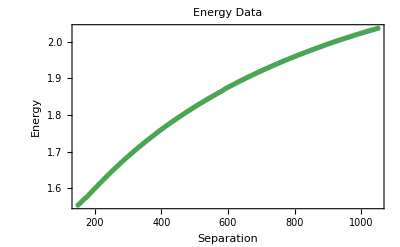

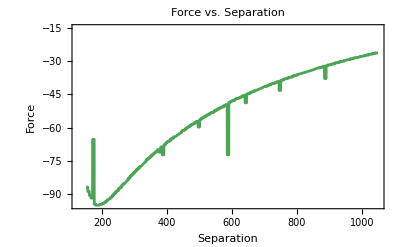

```mathematica
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion"];
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}]
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]]
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

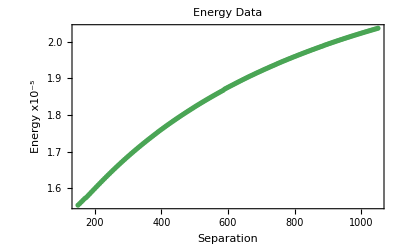

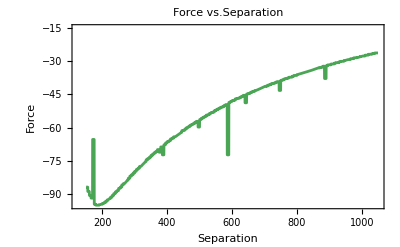

```mathematica
energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
```

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/FourthOrderSimpleTwoInclusion"];
Export["energyGraphnice.jpg", energyGraphnice, ImageResolution->1200]
```

energyGraphnice.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["energyGraphnice.png"]]]
```

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None];
prettyData
]
prettySurface["surface25.gpl"]
```

-Graphics3D-

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{{-300,300},{-150,150},Automatic}];
Show[prettyData,Graphics3D[{Black,Sphere[{137.5,0,400},10],Cylinder[{{-137.5,0,399},{-137.5,0,401}},10]}]]
]
prettySurface["surface25.gpl"]
```

-Graphics3D-